```mathematica
lista={{1,3,2},{-1,-5,8},{0,1,7}}
```

{{1,3,2},{-1,-5,8},{0,1,7}}

```mathematica
lista[[1]]
```

{1,3,2}

```mathematica
lista[[3]]
```

{0,1,7}

```mathematica
lista[[3,2]]
```

1

```mathematica
lista[[3,3]]
```

7

Zadatak 1. U tabeli su data pobednička vremena ženske plivačke štafete 4 x 100m slobodnim stilom.
		OI | 1996 | 2000 | 2004 | 2012 | 2016
vreme | 3:39.29 | 3:36.61 | 3:35.94 | 3:33.15 | 3:30.65
a) Naći polinom koji interpolira ove podatke.
b) Nacrtati ove podatke i interpolacioni polinom, zajedno na jednom grafiku.
c) Pomoću dobijenog polinoma proceniti pobedničko vreme na OI 2008. Ako je poznato da je na tim OI pobedničko vreme bilo 3:33.76, naći apsolutnu i relativnu grešku ove aproksimacije.

```mathematica
pod={{1996,3*60+39.29},{2000,3*60+36.61},{2004,3*60+35.94},{2012,3*60+33.15},{2016,3*60+30.65}}
```

{{1996,219.29},{2000,216.61},{2004,215.94},{2012,213.15},{2016,210.65}}

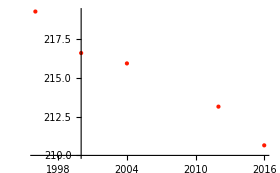

```mathematica
gr1=ListPlot[pod,PlotStyle->RGBColor[1,0.1,0]]
```

```mathematica
pv[t_]=InterpolatingPolynomial[pod,t]//Expand
```

3.5602×10^9-7.09018×10^6 t+5295.03 t^2-1.75749 t^3+0.00021875 t^4

```mathematica
pv[pod[[2,1]]]
```

216.61

```mathematica
pod[[2,2]]
```

216.61

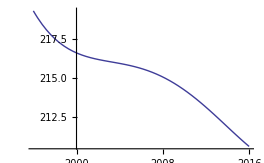

```mathematica
gr2=Plot[pv[t],{t,1996,2016}]
```

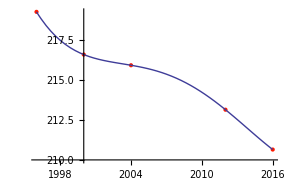

```mathematica
Show[gr1,gr2]
```

```mathematica
prib=pv[2008]
```

215.074

```mathematica
tacno=3*60+33.76
```

213.76

```mathematica
ag=Abs[prib-tacno]
```

1.314

```mathematica
rg=ag/Abs[tacno]
```

0.00614708

```mathematica
pv[2021]
```

209.625

```mathematica
tacnoTokyo=3*60+29.69
```

209.69

Zadatak 2. Napisati program koji za zadati skup od n+1 čvorova kreira interpolacioni polinom n-tog stepena u obliku p(x)=a_0+a_1 x+a_2 x^2+...+a_n x^n. Program testirati na problemu iz prethodnog zadatka.

```mathematica
a=({{-1, 2, 5, 6}, {0, 0, 2, -3}, {5, 6, 7, 8}, {9, 10, -9, -10}})
```

{{-1,2,5,6},{0,0,2,-3},{5,6,7,8},{9,10,-9,-10}}

```mathematica
a[[3,2]]
```

6

```mathematica
b=({{1}, {0}, {-5}, {3}})
```

{{1},{0},{-5},{3}}

```mathematica
Length[b]
```

4

```mathematica
LinearSolve[a,b]
```

{{-57/35},{43/35},{-12/35},{-8/35}}

```mathematica
intpol[pod_,x_]:=Module[{a,m,b,koef,baza},
					m=Length[pod];
					a=Table[1,{i,1,m},{j,1,m}];
					Do[
						a[[i,j]]=(pod[[i,1]])^(j-1),
						{i,1,m},{j,2,m}];
					b=Table[pod[[i,2]],{i,1,m}];
					koef=LinearSolve[a,b];
					baza=Table[x^i,{i,0,m-1}];
					koef.baza
					]
```

```mathematica
pod={{1996,3*60+39.29},{2000,3*60+36.61},{2004,3*60+35.94},{2012,3*60+33.15},{2016,3*60+30.65}}
```

{{1996,219.29},{2000,216.61},{2004,215.94},{2012,213.15},{2016,210.65}}

```mathematica
intpol[pod,t]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 1996., 3.98402×10^6, 7.9521×10^9, 1.58724×10^13}, « 3 », {1., 2016., « 12 », « 15 », 1.65182×10^13}} may contain significant numerical errors.

3.5602×10^9-7.09018×10^6 t+5295.03 t^2-1.75749 t^3+0.00021875 t^4

```mathematica
pod1={{0,3*60+39.29},{4,3*60+36.61},{8,3*60+35.94},{16,3*60+33.15},{20,3*60+30.65}}
```

{{0,219.29},{4,216.61},{8,215.94},{16,213.15},{20,210.65}}

```mathematica
pv[t_]=intpol[pod1,t]
```

219.29-1.18908 t+0.17025 t^2-0.0109948 t^3+0.00021875 t^4

```mathematica
pv[12]
```

215.074

Zadatak 3. Napisati program koji za zadati skup od n+1 čvorova kreira Lagranžov interpolacioni polinom n-tog stepena, ispisuje ga i iscrtava taj polinom, zajedno sa čvorovima. Program testirati na skupu {(1,2.2),(2,3.6),(4,8),(5,9),(7,11)}.

```mathematica
lp[cv_,x_]:=Module[{m,w},
			m=Length[cv];
			w=1;
			Do[
			w=w*(x-cv[[i,1]]),
			{i,1,m}];
			pol=0;
			Do[
				wi=w/(x-cv[[i,1]]);
				pol=pol+cv[[i,2]]*wi/(wi/.x->cv[[i,1]]),
			{i,1,m}];
			pol]
```

```mathematica
cv={{1,2.2},{2,3.6},{4,8},{5,9},{7,11}};
```

```mathematica
lagranz[x_]=lp[cv,x]
```

0.0305556 (-7+x) (-5+x) (-4+x) (-2+x)-0.12 (-7+x) (-5+x) (-4+x) (-1+x)+4/9 (-7+x) (-5+x) (-2+x) (-1+x)-3/8 (-7+x) (-4+x) (-2+x) (-1+x)+11/180 (-5+x) (-4+x) (-2+x) (-1+x)

```mathematica
lagranz[2.8]
```

5.54829

```mathematica
lp1[cv_,x_]:=Module[{m,w,gr1,gr2},
			m=Length[cv];
			w=1;
			Do[
			w=w*(x-cv[[i,1]]),
			{i,1,m}];
			pol=0;
			Do[
				wi=w/(x-cv[[i,1]]);
				pol=pol+cv[[i,2]]*wi/(wi/.x->cv[[i,1]]),
			{i,1,m}];
			Print[pol];
			gr1=ListPlot[cv];
			gr2=Plot[pol,{x,cv[[1,1]],cv[[m,1]]}];
			Show[gr1,gr2]
				]
```

0.0305556 (-7+x) (-5+x) (-4+x) (-2+x)-0.12 (-7+x) (-5+x) (-4+x) (-1+x)+4/9 (-7+x) (-5+x) (-2+x) (-1+x)-3/8 (-7+x) (-4+x) (-2+x) (-1+x)+11/180 (-5+x) (-4+x) (-2+x) (-1+x)

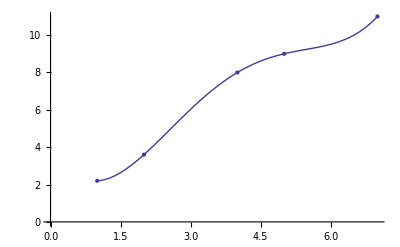

```mathematica
lp1[cv,x]
```